# Fibonacci Numbers

Helmut Knaust, Department of Mathematical Sciences, UTEP, El Paso TX 79968
hknaust@utep.edu
2/8/2017

Fibonacci[200] gives the 200th Fibonacci number:

```mathematica
Fibonacci[200]
```

280571172992510140037611932413038677189525

The command computes the first K Fibonacci numbers.

```mathematica
K=20;
Table[Fibonacci[n],{n,1,K}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

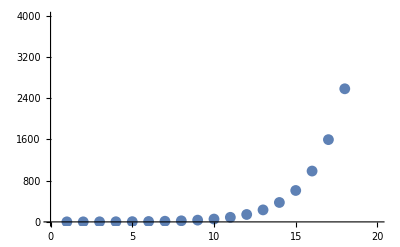

```mathematica
ListPlot[Table[Fibonacci[n],{n,1,K}]]
```

Fibonacci numbers grow nearly exponentially: The ratio between consecutive Fibonacci numbers approaches a limit:

```mathematica
Table[Fibonacci[n+1]/Fibonacci[n],{n,1,K}]//N
```

{1.,2.,1.5,1.66667,1.6,1.625,1.61538,1.61905,1.61765,1.61818,1.61798,1.61806,1.61803,1.61804,1.61803,1.61803,1.61803,1.61803,1.61803,1.61803}

The limit equals (1+√5)/2, called the “Golden Ratio”.

```mathematica
Print[(1+Sqrt[5])/2, " = " ,(1+Sqrt[5])/2.]
```

1/2 (1+√5) = 1.61803

Why? Let' s call this limit L. Then for “very large” n, L “=” f(n+1)/f(n), but also L “=” f(n)/f(n-1).

Thus L=(f(n+1))/(f(n))=(f(n))/(f(n-1)) 
Using the definition of Fibonacci numbers, we can substitute f(n+1)=f(n)+f(n-1) to obtain

(f(n)+f(n-1))/(f(n))=(f(n))/(f(n-1))

Simplifying and using the fact that L=(f(n))/(f(n-1)), we obtain the following quadratic equation for L:  1+L=1/L
This quadratic equation has one positive solution, namely (1+√5)/2